# Curso de Verão 2020 - Instituto de Física da USP

Prof. Dr. Alexandre Levine

DFMT - IFUSP

Minicurso “Técnicas para resolver problemas de física com Mathematica®”

Nesse minicurso vamos aprender como resolver problemas de física básica e avançada com sistema de álgebra computacional Mathematica®.

10 a 14 de fevereiro de 2020

## AULA 4 - MECÂNICA QUÂNTICA COM MATHEMATICA®

### Pacote de Onda

Vamos demonstrar graficamente a propagação de onda Gaussiana unidimensional de uma partícula livre.

A Física do Problema:

Partícula livre

V=0; -ℏ^2/(2m)(∂^2 ψ)/(∂x^2)=-ℏ/i(∂ψ)/(∂t)

Para essa equação é possível procurar solução na seguinte forma

```mathematica
Ψ[x_,t_]:=u[x]g[t];
-ℏ^2/(2m)D[Ψ[x,t],{x,2}]==-ℏ/ⅈ D[Ψ[x,t],{t,1}]
```

-(ℏ^2 g[t] u''[x])/(2 m)==ⅈ ℏ u[x] g'[t]

Separando variáveis com constante de separação ℏω, e k_0^2=2m ω/ℏ obtemos duas equações com soluções gerais abaixo

```mathematica
sol1=DSolve[ g'[t]==-I ω g[t],g[t],t]
sol2=DSolve[ u''[x]+Subscript[k, 0]^2 u[x]==0,u[x],x]
```

{{g[t]→ⅇ^(-ⅈ t ω) C[1]}}

{{u[x]→C[2] Cos[x k_0]+C[1] Sin[x k_0]}}

Para uma partícula livre uma solução particular é o pacote de onda Gaussiana unidimensional que pode ser escrito como:

Ψ(x, t)= [1/(2(πL^2(1+i ℏ/(2 mL^2)t))^2)]^(1/4)e^(i(k_0 x-ω_0 t))exp [-1/(4 L^2) (x-v_gr t)^2/(1+i ℏ/(2 mL^2)t)]

Onde m é a massa da partícula e L é a incerteza de posição no instante t=0. Também (p_0=ℏ k_0):

v_gr=(ℏ k_0)/m

ω_0=(ℏ k_0^2)/(2m)

```mathematica
ψ[x_,t_]:=(1/(2π L^2(1+ⅈ ℏ/(2m L^2)t)^2) )^(1/4)Exp[ⅈ(Subscript[k, 0] x - Subscript[ω, 0] t)] Exp[-1/(4 L^2)(x-Subscript[v, gr] t)^2/(1+ⅈ ℏ/(2 mL^2)t)];
$Assumptions=x ∈ Reals&& L >0&& Subscript[k, 0] >0;
ψ[x,0]//Simplify
```

(ⅇ^(-x^2/(4 L^2)+ⅈ x k_0) (1/L^2)^(1/4))/(2 π)^(1/4)

```mathematica
Subscript[P, 0]=Abs[ψ[x,0]]^2//Simplify
```

(ⅇ^(-x^2/(2 L^2)))/(L √(2 π))

Em que k_0 é o número de onda médio. A densidade da probabilidade de posição,  Ψ*(x, t)Ψ(x, t), pode ser expressada por:

P(x, t)= [1/(2πL^2(1+i ℏ^2/(4 m^2 L^4)t^2))]^(1/2)exp [-1/(2 L^2) (x-v_gr t)^2/(1+i ℏ^2/(4 m^2 L^4)t^2)]

Sendo x, t e P(x, t) medidos, respectivamente, em unidades de L, T e A, onde

T=(2m L^2)/ℏ

A=1/(√(2π L^2))

A equação para densidade da probabilidade então fica

P(x, t)= [1/(1+t^2)]^(1/2)exp [- (x-v t)^2/(2(1+t^2))]

Na qual

v=(2m L)/ℏ v_gr

Em unidades de L, a incerteza de posição ou a largura do pacote de onda no instante t é

Δ x(t) = √(1+t^2)

#### Solução com Mathematica

Existem várias maneiras de demonstrar a propagação do pacote de onda. A mais simples é utilizando a última equação, plotando Δx(t):

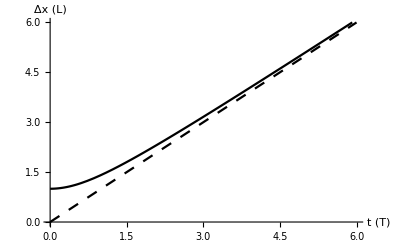

```mathematica
ClearAll["Global`*"]
style1[label_]:=Thread[Style[label,FontFamily->"Times"]]
Plot[{√(1+t^2),t},{t,0,6},
PlotRange->{0,6},PlotStyle->{{},{Dashing[{0.02,0.02}]}},AxesLabel->style1[{"t (T)","Δx (L)"}]]
```

Uma reta pontilhada é adicionada ao gráfico para mostrar que Δx(t)≈t para t≫1. A função “style1” define a formatação para os rótulos dos eixos.

Outro modo de mostrar a propagação de um pacote de onda é plotar P(x, t) para vários valores de t. Na demonstração seguinte, usamos v=1.

```mathematica
P[x_,t_]:=1/(√(1+t^2)) Exp[-(x-t)^2/(2(1+t^2))]
```

```mathematica
style2[label_]:=Thread[Style[label,FontFamily->"Times",Italic]]
```

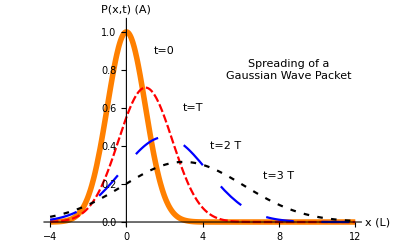

```mathematica
Plot[
Evaluate[Table[P[x,i],{i,0,3}]],{x,-4,12},
PlotStyle->{{Thickness[0.01],Orange},{Red},{Dashing[{0.05,0.05}],Blue},{Dashing[{0.01,0.015}]}},PlotRange->{0,1.05},AxesLabel->style2[{"x (L)","P(x,t) (A)"}],BaseStyle->{FontFamily->"Times"},Epilog->{Text["Spreading of a\nGaussian Wave Packet",{8.5,0.8}],Text[HoldForm[t=0],{2,0.9}],Text[HoldForm[t=T],{3.5,0.6}],Text[HoldForm[t=2T],{5.2,0.4}],Text[HoldForm[t=3T],{8,0.24}]}]
```

Ainda, mais um jeito de  plotar P(x, t) para vários valores de t:

```mathematica
g[n_]:=ParametricPlot3D[{x,n,P[x,n]},{x,-5.6,21},PlotPoints->100]
```

```mathematica
Show[
Table[
{g[i],Graphics3D[{Dashing[{0.01,0.01}],Line[{{-5.6,i,0},{21,i,0}}]}]},{i,0,7}],
PlotRange->{{-5.6,21},{0,7},{0,1}},ViewPoint->{2.230,2.323,1.040},BoxRatios->{1,2,0.5},Boxed->False,AxesLabel->style1[{"       x (L)","t (T) ","P(x,t) (A)"}],Ticks->{Automatic,Automatic,{0,1}}]
```

-Graphics3D-

Aqui, adicionamos a dimensão do tempo. Vamos observar a propagação de outra perspectiva:

```mathematica
Show[%,BoxRatios->{1,1,1},Boxed->True,ViewPoint->{0.017,3.375,0.245}]
```

-Graphics3D-

Podemos gerar uma animação da propagação do pacote de onda:

```mathematica
ListAnimate[
Table[
Show[
{g[i],
Graphics3D[{Dashing[{0.01,0.01}],Line[{{-5.6,i,0},{21,i,0}}]}]},
PlotRange->{{-5.6,21},{0,7},{0,1}},BoxRatios->{1,1,1},
ViewPoint->{0.017,3.375,0.245},
AxesLabel->style2[{"x (L)","t (T)","P(x,t) (A)"}],
Ticks->None],{i,0,7,1/8}]]
```

Finalmente, podemos também gerar uma animação da propagação que exiba o seu rastro:

```mathematica
ListAnimate[
Table[
Plot3D[P[x,t],{x,-5,14},{t,0,i/8+0.05},
PlotRange->{{-5,14},{0,5},{0,1}},ViewPoint->{0.017,3.375,0.245},BoxRatios->{1,1,1},PlotPoints->45,Ticks->None,AxesLabel->style2[{"x (L)","t (T)","P(x,t) (A)"}]],{i,0,40}]]
```

```mathematica
ClearAll[P,g]
```

### Poço Potencial Quadrado

Vamos determinar os estados ligados de uma partícula em um poço potencial quadrado, analiticamente e numericamente.

#### A Física do Problema

Consideremos uma partícula de massa m se movendo em um potencial unidimensional

V(x) = Piecewise[{{0, |x| >a}, {-V_0, |x|<a}}]

com V_0>0. A equação de Schrodinger independente do tempo é

-ℏ^2/(2m) (d^2 u(x))/(d x^2)+V(x)u(x) = E u(x)

Onde u(x) é a auto-função correspondente ao autovalor da energia E. Para estados ligados, E < 0.

#### Solução Analítica

Sejam

k = (√(2m|E|))/ℏ

q=(√(2m(V_0-|E| )))/ℏ

λ=(2m V_0 a^2)/ℏ^2

y=q a

Das três últimas equações, temos que o autovalor da energia E pode ser escrito como

E=-(1-y^2/λ)V_0

Que sugere que k pode ser escrito como

k=(√(λ-y^2))/a

Como consequência da simetria do potencial, a equação de Schrodinger independente do tempo tem dois grupos de soluções que são ligados no infinito. As soluções uniformes são

Piecewise[{{B e^(k x), x < -a}, {A cos q x
B e^(-k x), -a < x< a
x > a}}]

A continuidade das autofunções e suas derivadas em x = +a (ou x = -a) impõem as condições

B = A cos q a  e^(k a)

k = q tan q a

#### Solução Analítica com Mathematica

Em termos de λ e y , a última equação pode ser escrita como

(√(λ - y^2))/y=tan y

cujas raízes somente podem ser determinadas por meio de gráfico. Para isso, vamos seguir o procedimento abaixo:

```mathematica
ClearAll["Global`*"]
```

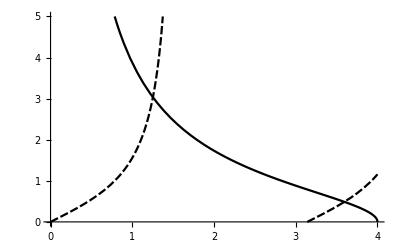

```mathematica
λ=16;
ClickPane[Plot[{(√(λ-y^2))/y,Tan[y]},{y,0,4},PlotRange->{0,5}],(yzcoord=#)&]
```

```mathematica
Dynamic[yzcoord]
```

```mathematica
startvalue={1.2721070114013822,3.5915582873092213}; (*Com o mouse, clique nas interseções e salve o primeiro valor da lista em uma nova lista chamada "startvalue", formando o velor representado aqui.*)
```

```mathematica
Table[FindRoot[(√(λ-y^2))/y==Tan[y],{y,startvalue[[i]]}],{i,Length[startvalue]}] (*"FindRoot" achará as raízes a partir dos valores das interseções do gráfico.*)
```

{{y→1.25235},{y→3.5953}}

```mathematica
{y[1],y[3]}=y/.%
```

{1.25235,3.5953}

Vamos determinar também as raízes da equação (√(λ-y^2))/y==-Cot[y] seguindo os mesmos procedimentos:

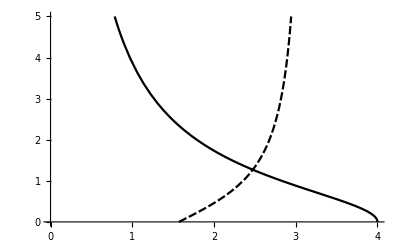

```mathematica
ClickPane[Plot[{(√(λ-y^2))/y,-Cot[y]},{y,0,4},PlotRange->{0,5}],(yzcoord=#)&]
```

```mathematica
FindRoot[(√(λ-y^2))/y==-Cot[y],{y,yzcoord[[1]]}]
```

{y→2.47458}

```mathematica
y[2]=y/.%
```

2.47458

Uma vez que as raízes são conhecidas, o autovalor correspondente da energia em termos de V_0 é dado por:

```mathematica
Ε[n_]:=-(1-y[n]^2/λ)Subscript[V, 0]
```

O potencial e os autovalores da energia são ilustrados em escala no gráfico abaixo:

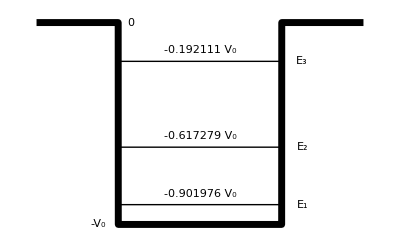

```mathematica
V[x_/;Abs[x]>1]:=0
V[x_/;Abs[x]<1]:=-1
Plot[V[x],{x,-2,2},
PlotStyle->Thickness[0.0125],PlotRange->{0.05,-1.05},Axes->False,Ticks->{None,Automatic},BaseStyle->{FontFamily->"Times",FontSize->12},
Epilog->({
Line[{{1,Ε[1]},{-1,Ε[1]}}],Text["E_1",{1.25,Ε[1]}],Text[ToString[Ε[1]/.Subscript[V, 0]->1]<>" V_0",{0,Ε[1]+0.055}],Line[{{1,Ε[2]},{-1,Ε[2]}}],Text["E_2",{1.25,Ε[2]}],
Text[ToString[Ε[2]/.Subscript[V, 0]->1]<>" V_0",{0,Ε[2]+0.055}],Line[{{1,Ε[3]},{-1,Ε[3]}}],Text["E_3",{1.25,Ε[3]}],Text[ToString[Ε[3]/.Subscript[V, 0]->1]<>" V_0",{0,Ε[3]+0.055}],Text["-V_0",{-1.25,-1}],Text["0",{-0.85,0}]}/.Subscript[V, 0]->1)]
```

Conhecendo os valores de y, para plotar as autofunções definiremos uma nova função para otimizar a entrada. O primeiro argumento da nova função vai aceitar y[1], y[2] ou y[3]. O segundo argumento aceitará uma autofunção par ou ímpar não normalizada.

```mathematica
eigenfunctionPlot[y_,u_]:=
Module[{normalizationConstant,normalizedu,energy},

(* Equation 6.4.6 *)
q=y;

(* Equation 6.4.8 *)
k=√(λ-y^2);

(* normalize the eigenfunction *)
normalizationConstant=1/(√NIntegrate[u[x]^2,{x,-∞,∞}]);
normalizedu[x_]=normalizationConstant u[x];

(* Equation 6.4.7 *)
energy=-(1-y^2/λ);

(* plot the eigenfunction *)
Plot[normalizedu[x],{x,-3,3},
Epilog->{Line[{{1,-1},{1,1}}],Line[{{-1,-1},{-1,1}}]},
Frame->True,FrameLabel->{"x (a)","u(x) (1/√a)"},ImageSize->{4 72,3 72},PlotLabel->"E = "<>ToString[energy]<>"V_0"]]
```

Faremos u[1][x], u[2][x] e u[3][x] as representações das autofunções não normalizadas correspondentes aos autovalores das energias E_1, E_2 e E_3, respectivamente.

```mathematica
uEven[x_]:=Piecewise[{{(Cos[q] Exp[k])Exp[k x],x<-1},{Cos[q x],Abs[x]≤1},{(Cos[q] Exp[k]) Exp[-k x],x>1}}]
uOdd[x_]:=Piecewise[{{(-Sin[q] Exp[k]) Exp[k x],x<-1},{Sin[q x],Abs[x]≤1},{(Sin[q] Exp[k]) Exp[-k x],x>1}}]
```

```mathematica
u[1]=u[3]=uEven;
u[2]=uOdd;
```

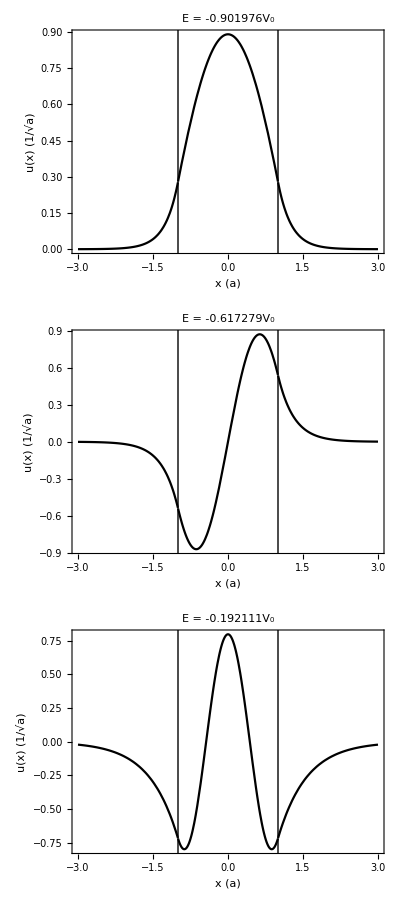

```mathematica
Column[Table[eigenfunctionPlot[y[n],u[n]],{n,1,3}]] (*Agora, plotamos as autofunções*)
```

```mathematica
ClearAll[yzcoord,V,q,k,y,uEven,uOdd,u,Ε,eigenfunctionPlot]
```

#### Solução Numérica

Apesar de não ser necessário especificar valores para o potencial em x=±a no caso da solução analítica da equação de Schrodinger independente do tempo, é prudente modificar a primeira equação para a solução numérica, incluindo valores de -V_0 para V(x) nesses pontos. Portanto,

V(x) = Piecewise[{{0, |x| >a}, {-V_0, |x|≤a}}]

Com V_0> 0. A segunda equação pode ser escrita como

(d^2 u(x))/(d x^2) = F(x) u(x)

Em que as distâncias são medidas em unidades de a - isto é, a=1, e

Piecewise[{{-λ e, |x| > 1}, {-λ(e+1), |x| ≤ 1}}]

Com o parâmetro de energia

e=E/V_0

Sendo que para estados ligados, 0> e>-1. Como já foi mencionado, a simetria do potencial implica que há duas classes de soluções, as pares e as ímpares. Para soluções pares, u’(0)=0. Sem perda de generalidade, faremos u(0) = 1 e determinaremos o seu valor apropriado depois, com a normalização da condição

∫_(-∞)^∞ u^2(x)ⅆ

Para as soluções ímpares, u(0) = 0. Vamos definir u’(0) = 1 e impor a condição de normalização nas autofunções depois. Para ambas as classes de soluções, só é necessário resolver numericamente a equação (d^2 u(x))/(d x^2) = F(x) u(x) para x≥0.

#### Solução Numérica com Mathematica

Seguindo essa equação, definimos

```mathematica
F[x_]:=Piecewise[{{-λ e,Abs[x]>1},{-λ(e+1),Abs[x]≤1}}]
```

Dado um valor para o parâmetro de energia e, podemos resolver a equação para a autofunção correspondente u(x). No entanto, as autofunções apenas são ligadas para certos valores discretos do parâmetro de energia. Isto é, u(∞) = 0. Para efeitos de análise numérica, escolheremos um ponto x = x_f a uma distância finita do poço de potencial, mas longe o suficiente para que  u(∞) = 0 possa ser substituído pela condição de u(x) próximo a zero em  x = x_f. A escolha de x_f depende de λ. Para λ=16, tomaremos meio arbitrariamente x_f = 4. Para achar os valores de e para o qual as autofunções tendem a zero em x =4, definimos a seguinte função:

```mathematica
eqnEven[r_?NumberQ]:=(
e=r;
sol=NDSolve[{u''[x]==F[x] u[x],u'[0]==0,u[0]==1},u,{x,0,4}];
u[4]/.sol[[1]])
```

Para soluções pares, e

```mathematica
eqnOdd[r_?NumberQ]:=(
e=r;
sol=NDSolve[{u''[x]==F[x] u[x],u'[0]==1,u[0]==0},u,{x,0,4}];
u[4]/.sol[[1]])
```

Para as soluções ímpares.

Com o valor para e de argumento, essas funções retornam o valor de u(4) e nomeiam como “sol” a solução para a segunda equação desta seção. Portanto, achar os valores de e para os quais as autofunções são iguais a zero em x = 4 é o mesmo que achar as raízes da equação eqnEven(r) = 0 para as soluções pares e eqnOdd(r) = 0 para as ímpares. Além disso, as soluções “sol” para esses valores de e fornecem as autofunções de estado ligado correspondentes. Para verificarmos se essas funções realmente se aproximam de zero em x = 4, usaremos “FindRoot [eqn[r] ==0, {r, r_0, r_1}]”, já que eqn(r) não é diferenciável. Precisamos, agora, de dois valores iniciais para r_0 e r_1 que sejam suficientemente próximos de uma raiz.

Considere as soluções pares. para determinar os valores apropriados para  r_0 e r_1, vamos gerar uma lista de {e_i, eqnEven(e_i)} com e_i variando de -1 a 0 em passos de 0.1. Para os estados ligados, temos:

```mathematica
Table[{i,eqnEven[i]},{i,-1,0,0.1}]
```

{{-1.,81377.4},{-0.9,-735.146},{-0.8,-16150.5},{-0.7,-12767.1},{-0.6,-7007.68},{-0.5,-3049.7},{-0.4,-1040.},{-0.3,-238.913},{-0.2,-6.5943},{-0.1,22.8457},{0.,8.42799}}

Procuramos nessa lista por dois valores consecutivos tais que (eqnEven(e_i)eqnEven(e_(i+1)))≤0 para servirem de valores iniciais para  r_0 e r_1. Para automatizar a seleção dos valores iniciais, particione a lista acima em sublistas não sobrepostas de dois pares
com um intervalo de 1:

```mathematica
Partition[%,2,1]
```

{{{-1.,81377.4},{-0.9,-735.146}},{{-0.9,-735.146},{-0.8,-16150.5}},{{-0.8,-16150.5},{-0.7,-12767.1}},{{-0.7,-12767.1},{-0.6,-7007.68}},{{-0.6,-7007.68},{-0.5,-3049.7}},{{-0.5,-3049.7},{-0.4,-1040.}},{{-0.4,-1040.},{-0.3,-238.913}},{{-0.3,-238.913},{-0.2,-6.5943}},{{-0.2,-6.5943},{-0.1,22.8457}},{{-0.1,22.8457},{0.,8.42799}}}

```mathematica
Select[%,(Sign[#[[1,2]]] Sign[#[[2,2]]]≤0)&]//N (*Selecione sublistas cujos valores dos segundos elementos têm sinais opostos*)
{#[[1,1]],#[[2,1]]}&/@% (*Escolha os pares dentro das sublistas escolhidas*)
```

{{{-1.,81377.4},{-0.9,-735.146}},{{-0.2,-6.5943},{-0.1,22.8457}}}

{{-1.,-0.9},{-0.2,-0.1}}

Podemos definir uma função para realizar todas as operações anteriores e localizar os valores iniciais:

```mathematica
initialValues[emin_,emax_,n_,eqn_]:=(
{#[[1,1]],#[[2,1]]}&/@(Select[Partition[Table[{i,eqn[i]},{i,emin,emax,(emax-emin)/n}],2,1],(Sign[#[[1,2]]] Sign[#[[2,2]]]≤0)&]//N))
```

```mathematica
evenvalues=initialValues[-1,0,10,eqnEven] (*Valores iniciais para soluções pares*)
```

{{-1.,-0.9},{-0.2,-0.1}}

```mathematica
oddvalues=initialValues[-1,0,10,eqnOdd] (*Valores iniciais para soluções ímpares*)
```

{{-0.7,-0.6}}

Para cada par de valores iniciais, FindRoot [eqn[r] ==0, {r, r_0, r_1}] responde com o valor do parâmetro de energia e e a solução do estado ligado correspondente (“sol”). Para os valores {-1., -0.9}, temos:

```mathematica
FindRoot[eqnEven[r]==0,{r,Sequence@@evenvalues[[1]]}]
```

{r→-0.901976}

```mathematica
Ε[1]=Subscript[V, 0] r/.% (*Autovalor de energia*)
```

-0.901976 V_0

```mathematica
u[1][x_/;0≤x≤4]=u[x]/.sol[[1]]; (*Autofunção associada*)
u[1][x_/;-4≤x<0]:=u[1][-x]
```

Para os valores iniciais {-o.7, -0.6}, temos:

```mathematica
FindRoot[eqnOdd[r]==0,{r,Sequence@@oddvalues[[1]]}]
```

{r→-0.617279}

```mathematica
Ε[2]=Subscript[V, 0] r/.%
```

-0.617279 V_0

```mathematica
u[2][x_/;0≤x≤4]=u[x]/.sol[[1]];
u[2][x_/;-4≤x<0]:=-u[2][-x]
```

E, para os valores iniciais {-0.2, -0.1}, temos:

```mathematica
FindRoot[eqnEven[r]==0,{r,Sequence@@evenvalues[[2]]}]
```

{r→-0.192105}

```mathematica
Ε[3]=Subscript[V, 0] r/.%
```

-0.192105 V_0

```mathematica
u[3][x_/;0≤x≤4]=u[x]/.sol[[1]];
u[3][x_/;-4≤x<0]:=u[3][-x]
```

Podemos produzir o diagrama, desenhado em escala, do potencial e os autovalores de energia:

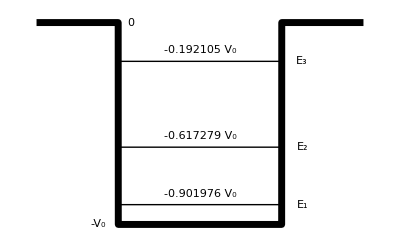

```mathematica
V[x_/;Abs[x]>1]:=0
V[x_/;Abs[x]<1]:=-1
Plot[V[x],{x,-2,2},
PlotStyle->Thickness[0.0125],PlotRange->{0.05,-1.05},Axes->False,Ticks->{None,Automatic},BaseStyle->{FontFamily->"Times",FontSize->12},
Epilog->({
Line[{{1,Ε[1]},{-1,Ε[1]}}],Text["E_1",{1.25,Ε[1]}],Text[ToString[Ε[1]/.Subscript[V, 0]->1]<>" V_0",{0,Ε[1]+0.055}],Line[{{1,Ε[2]},{-1,Ε[2]}}],Text["E_2",{1.25,Ε[2]}],
Text[ToString[Ε[2]/.Subscript[V, 0]->1]<>" V_0",{0,Ε[2]+0.055}],Line[{{1,Ε[3]},{-1,Ε[3]}}],Text["E_3",{1.25,Ε[3]}],Text[ToString[Ε[3]/.Subscript[V, 0]->1]<>" V_0",{0,Ε[3]+0.055}],Text["-V_0",{-1.25,-1}],Text["0",{-0.85,0}]}/.Subscript[V, 0]->1)]
```

E podemos plotar autofunções normalizadas:

```mathematica
plotFunc[u_]:=
Module[{normalizationConstant,normalizedu},
normalizationConstant=1/(√(2 NIntegrate[u[x]^2,{x,0,4}]));
normalizedu[x_]=normalizationConstant u[x];
Plot[normalizedu[x],{x,-3,3},
Epilog->{Line[{{1,-1},{1,1}}],Line[{{-1,-1},{-1,1}}]},
Frame->True,FrameLabel->{"x (a)","u(x) (1/√a)"},ImageSize->{4 72,3 72},PlotLabel->"E = "<>ToString[Ε[n]/.Subscript[V, 0]->1]<>"V_0"]]
```

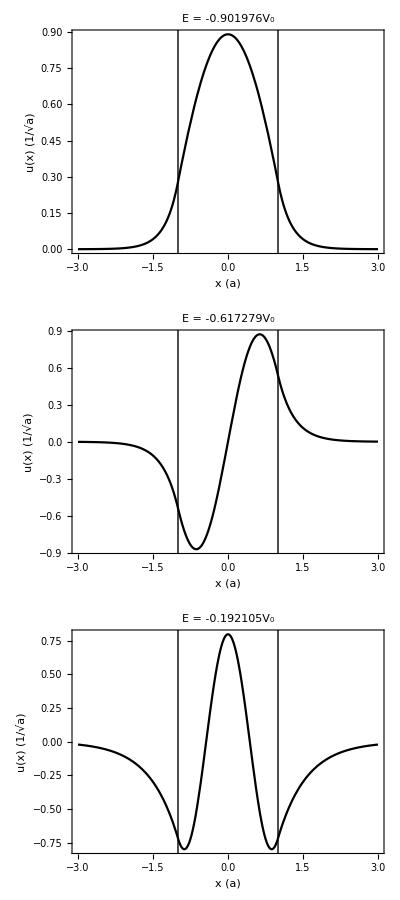

```mathematica
Column[Table[plotFunc[u[n]],{n,1,3}]]
```

Os diagramas são essencialmente os mesmos da seção anterior.

Nosso método numérico pode ser adaptado para outros potenciais unidimensionais, e ainda pode ser usado quando a equação de Schrodinger independente do tempo não puder ser resolvida nem pelas ferramentas analíticas mais poderosas. Contudo, algumas palavras de cautela são necessárias. Com este método numérico, é bem possível perder alguns autovalores de energia, mas essa armadilha pode ser evitada. Uma propriedade geral de estados ligados unidimensionais pode servir como segurança. Se os estados ligados estiverem organizados em ordem crescente de energias E1, E2. . . , En ,. . . , a enésima nona função possui n - 1 nós. Assim, se, por exemplo, as autofunções correspondentes a duas energias consecutivas em nosso espectro têm, respectivamente, n e n + 2 nós, devemos ter perdido um autovalor de energia. Ao determinar os valores iniciais apropriados r0 e r1 com initialValues[e_(i,)e_f, n, eqn],  considere fazer n maior ou e_f - e_i menor para varrer regiões com probabilidade de ter raízes.